```mathematica
ζp[s_,a_] :=D[HurwitzZeta[z,a],{z,1}]/.{z->s};
```

```mathematica
F[w_,a_] :=ζp[-1,a]+(w^2-a^2)/2 -(w-a)/2 (1+Log[2π])+NIntegrate[Log[Gamma[t]],{t,a,w}];
```

```mathematica
F[0.07605748908097676,0.15]
```

8.87485×10^-15

```mathematica
0.08318276518662693
```

```mathematica
ζp[-1,0.2]
```

0.0831828

```mathematica
FindRoot[ζp[-1,x]==0,{x,0.05}]
```

{x→0.0760575}

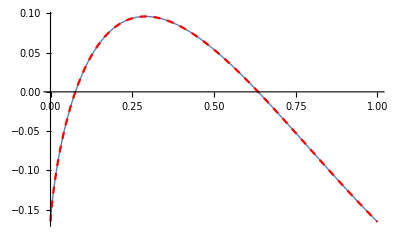

```mathematica
Plot[{F[x,0.15],ζp[-1,x]},{x,0.0001,1},PlotStyle->{Thick,Directive[Red,Dashed]}]
```

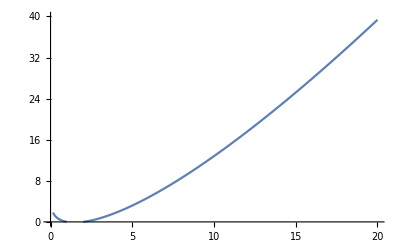

```mathematica
Plot[Log[Gamma[t]],{t,0.15,20},PlotRange->{{0,20},{0,40}}]
```

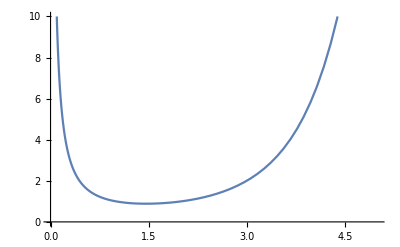

```mathematica
Plot[Gamma[t],{t,0,5},PlotRange->{{0,5},{0,10}}]
```